## Looking what remains if we put all constraints on the solutions

Firs we take the graph

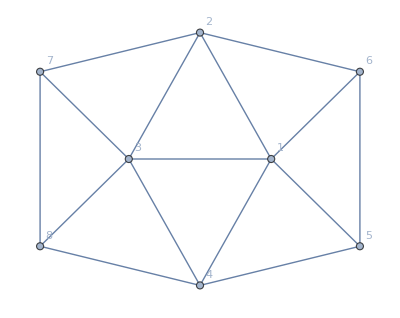

```mathematica
g=Graph[EdgeList[EdgeAdd[WheelGraph[6,VertexLabels->"Name"],{2 <->7,3 <->7,3 <->8,4 <->8,7 <->8
}]],GraphLayout->"SpringEmbedding",VertexLabels->"Name"]
```

From this graph we remove 3 edges to see what the remaining solutions are

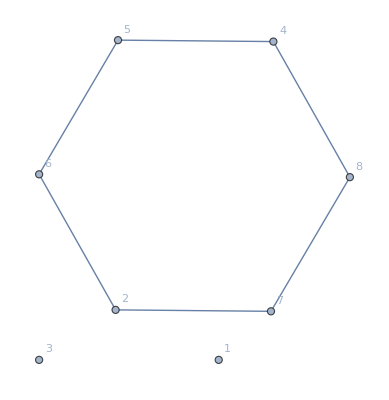

```mathematica
h=Graph[EdgeDelete[g,{3<->7,3<->8,1<->6,1<->5,2 <->1,2 <->3,4 <->1,4 <->3,1 <->3}],GraphLayout->"SpringEmbedding"]
```

```mathematica
solutions2=Select[FindFullFormula[h],SymbolLevel[#]==4&]
```

{v1x2x358x467,v1x2x3467x58,v1x28x35x467,v1x28x357x46,v1x28x3467x5,v1x28x346x57,v1x258x3x467,v1x25x38x467,v1x258x37x46,v1x258x367x4,v1x25x368x47,v1x258x36x47,v1x258x347x6,v1x258x346x7,v1x25x347x68,v1x25x3467x8,v1x258x34x67,v1x24x367x58,v1x24x368x57,v1x24x357x68,v1x24x358x67,v1x2358x4x67,v1x234x58x67,v1x234x57x68,v1x235x47x68,v1x2358x47x6,v1x238x467x5,v1x235x467x8,v1x2358x46x7,v1x23x467x58,v1x238x46x57,v18x2x35x467,v18x2x357x46,v18x2x3467x5,v18x2x346x57,v18x25x3x467,v18x25x37x46,v18x25x367x4,v18x25x36x47,v18x25x347x6,v18x25x346x7,v18x25x34x67,v18x24x367x5,v18x24x36x57,v18x24x357x6,v18x24x35x67,v18x235x4x67,v18x234x5x67,v18x234x57x6,v18x235x47x6,v18x23x467x5,v18x235x46x7,v18x23x46x57,v17x2x358x46,v17x2x346x58,v17x28x35x46,v17x28x346x5,v17x258x3x46,v17x25x38x46,v17x25x368x4,v17x258x36x4,v17x258x34x6,v17x25x346x8,v17x25x34x68,v17x24x368x5,v17x24x36x58,v17x24x358x6,v17x24x35x68,v17x235x4x68,v17x2358x4x6,v17x234x5x68,v17x234x58x6,v17x238x46x5,v17x235x46x8,v17x23x46x58,v168x2x357x4,v167x2x358x4,v16x2x358x47,v168x2x35x47,v168x2x347x5,v16x2x347x58,v167x2x34x58,v168x2x34x57,v16x28x357x4,v167x28x35x4,v16x28x35x47,v16x28x347x5,v167x28x34x5,v16x28x34x57,v167x258x3x4,v16x258x3x47,v168x25x3x47,v167x25x38x4,v16x25x38x47,v16x258x37x4,v168x25x37x4,v16x258x34x7,v168x25x34x7,v16x25x347x8,v167x25x34x8,v167x24x3x58,v168x24x3x57,v167x24x38x5,v16x24x38x57,v168x24x37x5,v16x24x37x58,v16x24x358x7,v168x24x35x7,v16x24x357x8,v167x24x35x8,v167x238x4x5,v168x235x4x7,v167x235x4x8,v16x2358x4x7,v167x23x4x58,v16x238x4x57,v168x23x4x57,v168x234x5x7,v167x234x5x8,v16x234x58x7,v16x234x57x8,v16x238x47x5,v168x23x47x5,v16x235x47x8,v16x23x47x58,v158x2x3x467,v15x2x38x467,v157x2x38x46,v158x2x37x46,v158x2x367x4,v157x2x368x4,v15x2x368x47,v158x2x36x47,v158x2x347x6,v158x2x346x7,v157x2x346x8,v15x2x347x68,v157x2x34x68,v15x2x3467x8,v158x2x34x67,v15x28x3x467,v157x28x3x46,v15x28x37x46,v15x28x367x4,v157x28x36x4,v15x28x36x47,v15x28x347x6,v157x28x34x6,v15x28x346x7,v15x28x34x67,v157x24x3x68,v158x24x3x67,v157x24x38x6,v15x24x38x67,v158x24x37x6,v15x24x37x68,v15x24x368x7,v158x24x36x7,v15x24x367x8,v157x24x36x8,v157x238x4x6,v157x23x4x68,v15x238x4x67,v158x23x4x67,v158x234x6x7,v157x234x6x8,v15x234x68x7,v15x234x67x8,v15x238x47x6,v158x23x47x6,v15x23x47x68,v15x238x46x7,v158x23x46x7,v15x23x467x8,v157x23x46x8,v1467x2x3x58,v1467x2x38x5,v146x2x38x57,v146x2x37x58,v147x2x368x5,v14x2x367x58,v147x2x36x58,v14x2x368x57,v147x2x358x6,v146x2x358x7,v146x2x357x8,v14x2x357x68,v147x2x35x68,v1467x2x35x8,v14x2x358x67,v1467x28x3x5,v146x28x3x57,v146x28x37x5,v14x28x367x5,v147x28x36x5,v14x28x36x57,v14x28x357x6,v147x28x35x6,v146x28x35x7,v14x28x35x67,v147x258x3x6,v146x258x3x7,v147x25x3x68,v1467x25x3x8,v14x258x3x67,v147x25x38x6,v146x25x38x7,v14x25x38x67,v14x258x37x6,v146x25x37x8,v14x25x37x68,v14x25x368x7,v14x258x36x7,v14x25x367x8,v147x25x36x8,v147x238x5x6,v146x238x5x7,v147x23x5x68,v1467x23x5x8,v14x238x5x67,v147x235x6x8,v146x235x7x8,v14x235x68x7,v14x235x67x8,v14x2358x6x7,v147x23x58x6,v146x23x58x7,v14x23x58x67,v14x238x57x6,v146x23x57x8,v14x23x57x68,v1367x2x4x58,v1358x2x4x67,v1368x2x4x57,v1357x2x4x68,v134x2x58x67,v134x2x57x68,v1368x2x47x5,v1347x2x5x68,v135x2x47x68,v1358x2x47x6,v1347x2x58x6,v136x2x47x58,v138x2x467x5,v13467x2x5x8,v135x2x467x8,v1358x2x46x7,v1346x2x58x7,v13x2x467x58,v137x2x46x58,v1357x2x46x8,v1346x2x57x8,v138x2x46x57,v1367x28x4x5,v135x28x4x67,v1357x28x4x6,v136x28x4x57,v134x28x5x67,v134x28x57x6,v1347x28x5x6,v136x28x47x5,v135x28x47x6,v1346x28x5x7,v13x28x467x5,v137x28x46x5,v135x28x46x7,v13x28x46x57,v137x258x4x6,v136x258x4x7,v1368x25x4x7,v137x25x4x68,v1367x25x4x8,v13x258x4x67,v138x25x4x67,v134x258x6x7,v134x25x68x7,v134x25x67x8,v1347x25x6x8,v13x258x47x6,v138x25x47x6,v136x25x47x8,v13x25x47x68,v1346x25x7x8,v13x258x46x7,v138x25x46x7,v13x25x467x8,v137x25x46x8,v1368x24x5x7,v137x24x5x68,v1367x24x5x8,v138x24x5x67,v135x24x68x7,v135x24x67x8,v1358x24x6x7,v137x24x58x6,v136x24x58x7,v13x24x58x67,v1357x24x6x8,v138x24x57x6,v136x24x57x8,v13x24x57x68,v1258x3x4x67,v124x3x58x67,v124x3x57x68,v125x3x47x68,v1258x3x47x6,v128x3x467x5,v125x3x467x8,v1258x3x46x7,v12x3x467x58,v128x3x46x57,v123x4x58x67,v123x4x57x68,v123x47x5x68,v123x47x58x6,v123x467x5x8,v123x46x58x7,v123x46x57x8,v1238x4x5x67,v125x38x4x67,v1238x4x57x6,v124x38x5x67,v124x38x57x6,v1238x47x5x6,v125x38x47x6,v1238x46x5x7,v12x38x467x5,v125x38x46x7,v12x38x46x57,v125x37x4x68,v1258x37x4x6,v124x37x5x68,v124x37x58x6,v128x37x46x5,v125x37x46x8,v12x37x46x58,v128x367x4x5,v125x368x4x7,v125x367x4x8,v1258x36x4x7,v12x367x4x58,v12x368x4x57,v128x36x4x57,v124x368x5x7,v124x367x5x8,v124x36x58x7,v124x36x57x8,v12x368x47x5,v128x36x47x5,v125x36x47x8,v12x36x47x58,v12358x4x6x7,v128x357x4x6,v1235x4x68x7,v12x357x4x68,v1235x4x67x8,v12x358x4x67,v128x35x4x67,v124x358x6x7,v124x357x6x8,v124x35x68x7,v124x35x67x8,v1235x47x6x8,v12x358x47x6,v128x35x47x6,v12x35x47x68,v1235x46x7x8,v12x358x46x7,v128x35x46x7,v12x35x467x8,v12x357x46x8,v128x347x5x6,v128x346x5x7,v1234x5x68x7,v12x347x5x68,v12x3467x5x8,v1234x5x67x8,v128x34x5x67,v125x347x6x8,v125x346x7x8,v125x34x68x7,v125x34x67x8,v1258x34x6x7,v1234x58x6x7,v12x347x58x6,v12x346x58x7,v12x34x58x67,v1234x57x6x8,v128x34x57x6,v12x346x57x8,v12x34x57x68}

```mathematica
Length[solutions2]
```

391

```mathematica
SymbolToColoring2[s_]:=Block[{sets=SymbolToSets[s],result={},colors={Red,Blue,Yellow,Green,Orange },colorpos=1},
Table[
Table[
AppendTo[result,v->Framed[v,FrameStyle->colors[[colorpos]]]]
,{v,block}
];
colorpos++;
If[colorpos>Length[colors],colorpos=1];
,{block,sets}
];
result
]
```

```mathematica
BoolToInt[b_]:=If[b,1,0]
```

```mathematica
Right1[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{3,7}}]
```

```mathematica
Right2[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{3,8}}]
```

```mathematica
Right3[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{3,4}}]
```

```mathematica
Right4[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,3}}]
```

```mathematica
Right5[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{2,3}}]
```

```mathematica
Left1[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,6}}]
```

```mathematica
Left2[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,5}}]
```

```mathematica
Left3[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,2}}]
```

```mathematica
Left4[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,3}}]
```

```mathematica
Left5[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,4}}]
```

```mathematica
RightHasPattern[s_]:=PartitionHasPattern[SymbolToSets[s],{{2},{3,5},{4,6}}]||
PartitionHasPattern[SymbolToSets[s],{{3},{2,5},{4,6}}]||
PartitionHasPattern[SymbolToSets[s],{{4},{3,6},{2,5}}]||
PartitionHasPattern[SymbolToSets[s],{{5},{2,4},{3,6}}]||
PartitionHasPattern[SymbolToSets[s],{{6},{2,4},{3,5}}]
```

```mathematica
LeftHasPattern[s_]:=PartitionHasPattern[SymbolToSets[s],{{1},{2,8},{4,7}}]||
PartitionHasPattern[SymbolToSets[s],{{2},{1,8},{4,7}}]||
PartitionHasPattern[SymbolToSets[s],{{4},{1,7},{2,8}}]||
PartitionHasPattern[SymbolToSets[s],{{7},{2,4},{1,8}}]||
PartitionHasPattern[SymbolToSets[s],{{8},{2,4},{1,7}}]
```

```mathematica
ColorList[labels_,flags_]:=Select[Table[If[flags[[k]]==1,Null,Style[labels[[k]],Red]],{k,Length[flags]}],#=!=Null&]
```

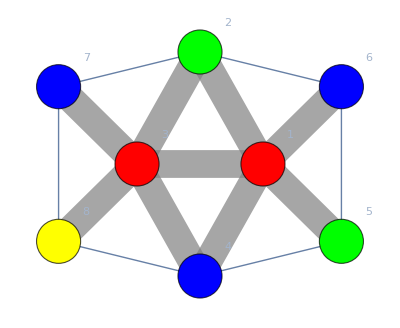
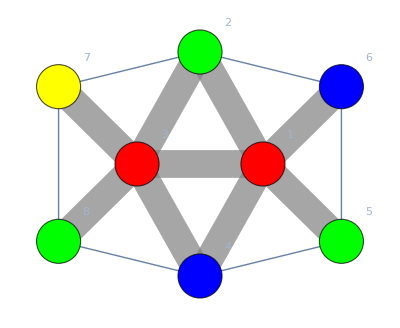
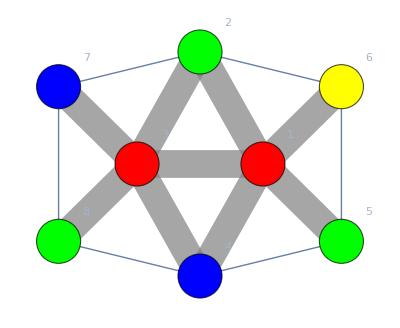
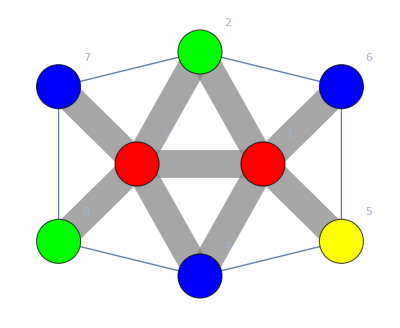
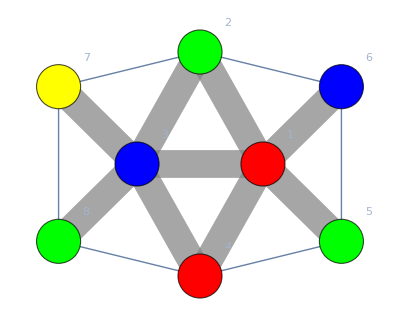
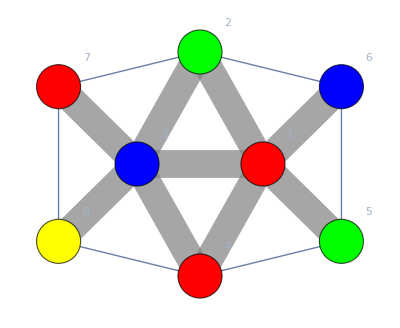
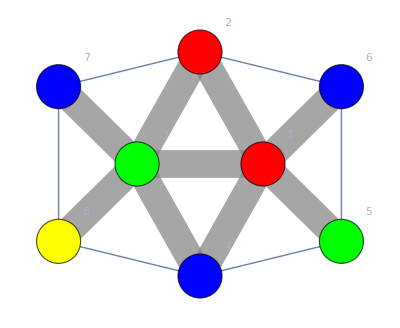
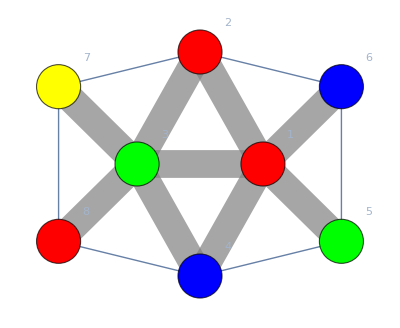
{8,True,759,13♁25♁467♁8,-Graphics-,{3==1,1==3},False,True}
{8,True,759,13♁258♁46♁7,-Graphics-,{3==1,1==3},False,True}
{8,True,759,13♁258♁47♁6,-Graphics-,{3==1,1==3},True,False}
{8,True,759,13♁28♁467♁5,-Graphics-,{3==1,1==3},True,False}
{9,True,511,14♁258♁36♁7,-Graphics-,{1==4},False,True}
{9,True,511,147♁25♁36♁8,-Graphics-,{1==4},False,True}
{9,True,895,12♁35♁467♁8,-Graphics-,{1==2},False,True}
{9,True,895,128♁35♁46♁7,-Graphics-,{1==2},False,True}
{9,True,959,15♁28♁3♁467,-Graphics-,{1==5},True,False}
{9,True,959,15♁28♁36♁47,-Graphics-,{1==5},True,False}
{9,True,959,157♁24♁3♁68,-Graphics-,{1==5},True,False}
{9,True,959,157♁28♁3♁46,-Graphics-,{1==5},True,False}
{9,True,959,157♁28♁36♁4,-Graphics-,{1==5},True,False}
{9,True,959,158♁2♁3♁467,-Graphics-,{1==5},True,False}
{9,True,959,158♁2♁36♁47,-Graphics-,{1==5},True,False}
{9,True,959,158♁24♁3♁67,-Graphics-,{1==5},True,False}
{9,True,991,16♁258♁3♁47,-Graphics-,{1==6},True,False}
{9,True,991,16♁28♁35♁47,-Graphics-,{1==6},True,False}
{9,True,991,167♁24♁3♁58,-Graphics-,{1==6},True,False}
{9,True,991,167♁258♁3♁4,-Graphics-,{1==6},True,False}
{9,True,991,167♁28♁35♁4,-Graphics-,{1==6},True,False}
{9,True,991,168♁2♁35♁47,-Graphics-,{1==6},True,False}
{9,True,991,168♁24♁3♁57,-Graphics-,{1==6},True,False}
{9,True,991,168♁25♁3♁47,-Graphics-,{1==6},True,False}
{9,True,1007,18♁23♁467♁5,-Graphics-,{3==2},True,False}
{9,True,1007,18♁235♁47♁6,-Graphics-,{3==2},True,False}
{9,True,1019,17♁258♁34♁6,-Graphics-,{3==4},True,False}
{9,True,1019,17♁28♁346♁5,-Graphics-,{3==4},True,False}
{9,True,1021,1♁2♁358♁467,-Graphics-,{3==8},False,True}
{9,True,1021,1♁24♁358♁67,-Graphics-,{3==8},False,True}
{9,True,1021,1♁24♁368♁57,-Graphics-,{3==8},False,True}
{9,True,1021,1♁25♁368♁47,-Graphics-,{3==8},False,True}
{9,True,1021,1♁25♁38♁467,-Graphics-,{3==8},False,True}
{9,True,1021,17♁2♁358♁46,-Graphics-,{3==8},False,True}
{9,True,1021,17♁25♁368♁4,-Graphics-,{3==8},False,True}
{9,True,1021,17♁25♁38♁46,-Graphics-,{3==8},False,True}
{9,True,1022,1♁24♁357♁68,-Graphics-,{3==7},False,True}
{9,True,1022,1♁24♁367♁58,-Graphics-,{3==7},False,True}
{9,True,1022,1♁258♁367♁4,-Graphics-,{3==7},False,True}
{9,True,1022,1♁258♁37♁46,-Graphics-,{3==7},False,True}
{9,True,1022,1♁28♁357♁46,-Graphics-,{3==7},False,True}
{9,True,1022,18♁2♁357♁46,-Graphics-,{3==7},False,True}
{9,True,1022,18♁25♁367♁4,-Graphics-,{3==7},False,True}
{9,True,1022,18♁25♁37♁46,-Graphics-,{3==7},False,True}

```mathematica
TableForm[Select[Map[With[{d=FromDigits[Reverse[{
BoolToInt[!Right1[#]],
BoolToInt[!Right2[#]],
BoolToInt[!Right3[#]],
BoolToInt[!Right4[#]],
BoolToInt[!Right5[#]],
BoolToInt[!Left1[#]],
BoolToInt[!Left2[#]],
BoolToInt[!Left3[#]],
BoolToInt[!Left4[#]],
BoolToInt[!Left5[#]]
}],2]},{Total[IntegerDigits[d,2]],
Xor[LeftHasPattern[#] ,
RightHasPattern[#]],
d,
SymbolToLabel[#],
Graph[ColorGraph[g,SymbolToSets[#]],EdgeStyle->Map[#->Directive[Thickness[0.05],Gray]&,{3<->7,3<->8,1<->6,1<->5,2 <->1,2 <->3,4 <->1,4 <->3,1 <->3}]],
ColorList[{"3==7","3==8","3==4","3==1","3==2","1==6","1==5","1==2","1==3","1==4"},Reverse[PadLeft[IntegerDigits[d,2],10]]],
LeftHasPattern[#],
RightHasPattern[#]
}]&,Sort[solutions2,CompareSymbols]
]//Sort,(#[[1]]==9||#[[3]]==759)&&#[[2]]&], TableSpacing->{1, 10}, TableDepth->1]
```

```mathematica
Map[SetsToSymbol,FindFiner [SymbolToSets[v157x24x36x8]]]
```

{v1x24x36x57x8,v15x24x36x7x8,v17x24x36x5x8,v157x2x36x4x8,v157x24x3x6x8}

```mathematica
DeleteDuplicates[Flatten[Map[Map[SetsToSymbol,FindFiner [SymbolToSets[#]]]&,{v157x24x36x8,v167x24x35x8,v17x24x358x6,v18x24x357x6}]]]
```

{v1x24x36x57x8,v15x24x36x7x8,v17x24x36x5x8,v157x2x36x4x8,v157x24x3x6x8,v1x24x35x67x8,v16x24x35x7x8,v17x24x35x6x8,v167x2x35x4x8,v167x24x3x5x8,v1x24x358x6x7,v17x2x358x4x6,v17x24x3x58x6,v17x24x38x5x6,v1x24x357x6x8,v18x2x357x4x6,v18x24x3x57x6,v18x24x35x6x7,v18x24x37x5x6}

```mathematica
GraphForSymbols[s_]:=FormulaGraphReverse[Join[s,DeleteDuplicates[Flatten[Map[Map[SetsToSymbol,FindFiner [SymbolToSets[#]]]&,s]]]]]
```

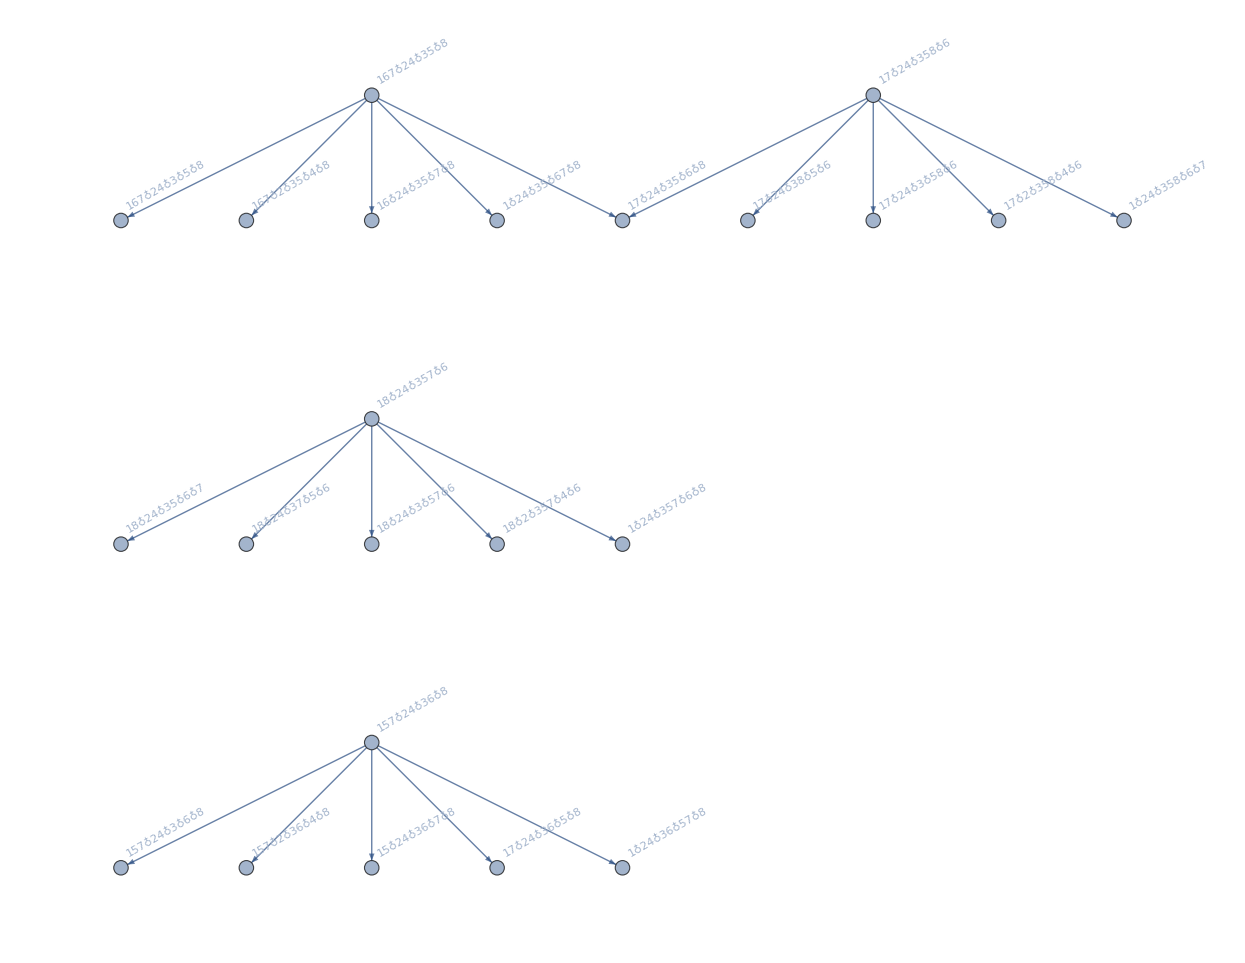

```mathematica
GraphForSymbols[{v157x24x36x8,v167x24x35x8,v17x24x358x6,v18x24x357x6}]
```